# (1) Evolution

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Performance in one condition

```mathematica
runnumber=100;
threshold=0.0;
max=9999;
```

78

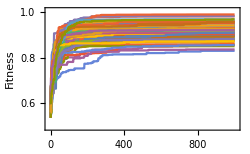

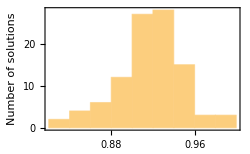

```mathematica
exp="../cSrc/15";
maxfit=0.0;
maxind =-1;
allgens={};
allfit={};
bestgen={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens=Append[allgens,y[[2]]];
allfit=Append[allfit,Last[y[[2]]]];
If[Last[y[[2]]]>maxfit,maxfit=Last[y[[2]]];maxind=i;];
If[Last[y[[2]]]>threshold,
file = StringJoin[exp,"/",ToString[i], "/best.gen.dat"];
x = Flatten[Import[file]];
bestgen=Append[bestgen,x];
];
];

maxind
ListLinePlot[Sqrt[allgens],PlotRange->{{-10,1010},{0.49,1.01}},Frame->True,FrameLabel->{"Generations","Fitness"},ImageSize->250]
(*Export["b.eps",%]*)
Histogram[Sqrt[allfit],Frame->True,FrameLabel->{"Fitness","Number of solutions"},ImageSize->250]
(*Export["b_hist.eps",%]*)
```

```mathematica
Sort[Table[{x-1,allfit[[x]]},{x,1,runnumber}],#1[[2]]>#2[[2]]&]
```

{{78,0.981142},{64,0.966916},{3,0.965106},{99,0.939509},{96,0.939064},{93,0.922791},{4,0.920747},{95,0.918794},{61,0.91651},{65,0.914989},{2,0.912333},{28,0.911039},{11,0.906447},{55,0.900701},{7,0.899974},{30,0.897212},{81,0.888791},{58,0.888518},{87,0.887827},{13,0.886628},{31,0.884295},{66,0.883453},{15,0.883145},{45,0.879246},{24,0.875577},{34,0.874391},{49,0.874365},{19,0.87328},{75,0.871915},{16,0.869867},{12,0.869821},{25,0.869483},{76,0.868354},{43,0.868314},{33,0.865869},{85,0.864152},{69,0.862868},{67,0.862131},{42,0.859727},{91,0.859722},{52,0.859639},{36,0.859636},{0,0.858642},{72,0.857894},{54,0.85662},{46,0.849329},{98,0.848336},{62,0.847354},{89,0.846642},{82,0.841427},{32,0.839617},{6,0.839098},{77,0.837338},{79,0.836801},{57,0.83071},{74,0.829498},{90,0.828259},{88,0.82651},{56,0.82612},{37,0.825599},{68,0.825468},{63,0.824289},{53,0.824111},{26,0.823122},{23,0.820342},{35,0.820302},{40,0.820256},{5,0.819799},{18,0.819191},{70,0.819106},{51,0.818735},{38,0.817541},{14,0.813573},{47,0.813501},{22,0.811954},{60,0.811241},{29,0.808995},{9,0.808516},{20,0.805335},{50,0.804807},{10,0.802578},{44,0.79939},{80,0.796815},{21,0.796154},{17,0.786774},{59,0.781043},{94,0.776257},{73,0.774755},{41,0.769672},{92,0.769488},{27,0.764223},{97,0.760708},{1,0.755591},{48,0.741365},{39,0.735787},{8,0.733386},{86,0.730912},{84,0.723335},{83,0.698836},{71,0.688704}}

```mathematica
(*DistributionChart[Transpose[bestgen],ChartStyle->"SouthwestColors",ChartElementFunction->"HistogramDensity",Frame->True,AspectRatio->1/10,FrameLabel->{"Parameters","Genotype value"},ImageSize->1200]
Export["Parameters.eps",%]*)
```

## Performance across circuit size (N=3,..,15)

```mathematica
runnumber=100;
```

```mathematica
exp="../cSrc/3";
allgens3={};
allfit3={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens3=Append[allgens3,y[[2]]];
allfit3=Append[allfit3,Last[y[[2]]]];
];

exp="../cSrc/5";
allgens5={};
allfit5={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens5=Append[allgens5,y[[2]]];
allfit5=Append[allfit5,Last[y[[2]]]];
];

exp="../cSrc/7";
allgens7={};
allfit7={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens7=Append[allgens7,y[[2]]];
allfit7=Append[allfit7,Last[y[[2]]]];
];

exp="../cSrc/9";
allgens9={};
allfit9={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens9=Append[allgens9,y[[2]]];
allfit9=Append[allfit9,Last[y[[2]]]];
];

exp="../cSrc/11";
allgens11={};
allfit11={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens11=Append[allgens11,y[[2]]];
allfit11=Append[allfit11,Last[y[[2]]]];
];

exp="../cSrc/13";
allgens13={};
allfit13={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens13=Append[allgens13,y[[2]]];
allfit13=Append[allfit13,Last[y[[2]]]];
];

exp="../cSrc/15";
allgens15={};
allfit15={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgens15=Append[allgens15,y[[2]]];
allfit15=Append[allfit15,Last[y[[2]]]];
];
```

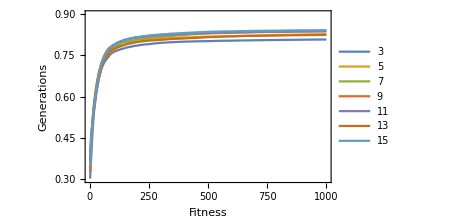

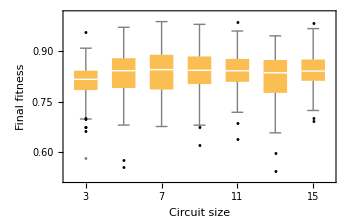

```mathematica
ListLinePlot[{Mean[allgens3],Mean[allgens5],Mean[allgens7],Mean[allgens9],Mean[allgens11],Mean[allgens13],Mean[allgens15]},PlotLegends->{"3","5","7","9","11","13","15"},PlotRange->{Automatic,{0.3,0.9}},Frame->True,ImageSize->350,FrameLabel->{"Fitness","Generations"}]
BoxWhiskerChart[{allfit3,allfit5,allfit7,allfit9,allfit11,allfit13,allfit15},"Outliers",ChartLabels->{"3","5","7","9","11","13","15"},Frame->True,FrameLabel->{"Circuit size","Final fitness"},ImageSize->350]
```

## Performance across circuit size (N=3,..,15)

```mathematica
runnumber=100;
```

```mathematica
exp="../EvolutionData/C7";
allgensC7={};
allfitC7={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC7=Append[allgensC7,y[[2]]];
allfitC7=Append[allfitC7,Last[y[[2]]]];
];

exp="../EvolutionData/C15";
allgensC15={};
allfitC15={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensC15=Append[allgensC15,y[[2]]];
allfitC15=Append[allfitC15,Last[y[[2]]]];
];

exp="../EvolutionData/D7";
allgensD7={};
allfitD7={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD7=Append[allgensD7,y[[2]]];
allfitD7=Append[allfitD7,Last[y[[2]]]];
];

exp="../EvolutionData/D15";
allgensD15={};
allfitD15={};
For[i=0, i<runnumber, i++,
file = StringJoin[exp,"/",ToString[i], "/fitness.dat"];
x = Import[file];
y = Transpose[x];
allgensD15=Append[allgensD15,y[[2]]];
allfitD15=Append[allfitD15,Last[y[[2]]]];
];
```

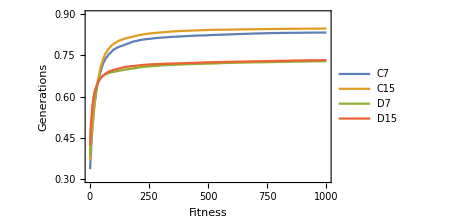

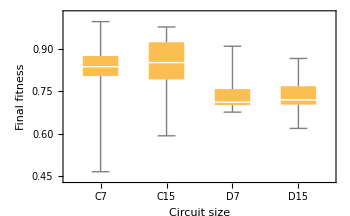

```mathematica
ListLinePlot[{Mean[allgensC7],Mean[allgensC15],Mean[allgensD7],Mean[allgensD15]},PlotLegends->{"C7","C15","D7","D15"},PlotRange->{Automatic,{0.3,0.9}},Frame->True,ImageSize->350,FrameLabel->{"Fitness","Generations"}]
BoxWhiskerChart[{allfitC7,allfitC15,allfitD7,allfitD15},ChartLabels->{"C7","C15","D7","D15"},Frame->True,FrameLabel->{"Circuit size","Final fitness"},ImageSize->350]
```